```mathematica
S=Import["/home/artem/projects/solver/build/Solve/Solve0spectrum_99.txt", "table"];
S=Table[{3*10^10/S[[i,1]]*10^7,S[[i,2]]*10^29}, {i,2,Length[S]}];

S0=Import["/home/artem/projects/solver/build/Solve/Solve0spectrumv99.txt", "table"];
S0=Table[{3*10^10/S0[[i,1]]*10^7,S0[[i,2]]*10^29}, {i,2,Length[S]}];
```

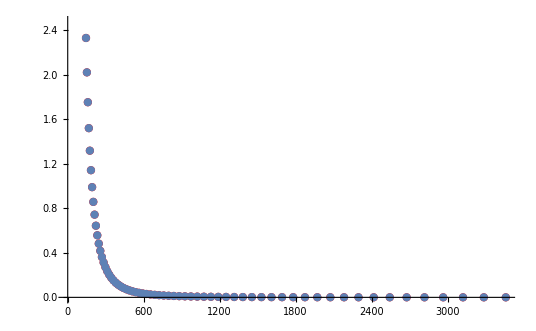

```mathematica
Show[
ListPlot[{Table[S[[i]],{i,100,170}]}, PlotStyle->Red],
ListPlot[{Table[S0[[i]],{i,100,170}]}]
]
```

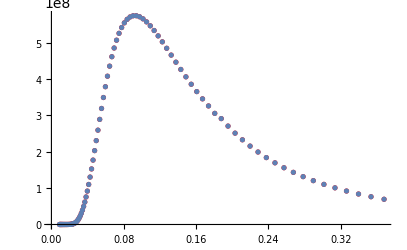

```mathematica
Show[
ListPlot[{Table[S[[i]],{i,300,400}]}, PlotStyle->Red],
ListPlot[{Table[S0[[i]],{i,300,400}]}]
]
```

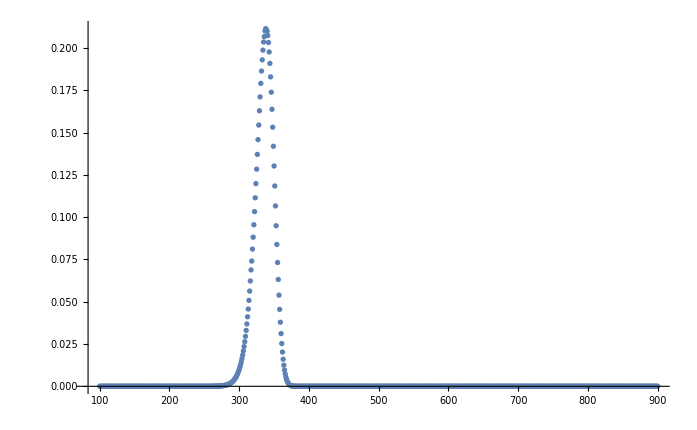

```mathematica
ListPlot[Table[{i,S[[i,2]]-S0[[i,2]]},{i,100,900}],PlotRange->All]
```

```mathematica
{S[[333]],(S[[333,2]]-S0[[333,2]])/S[[333,2]]}
```

{{0.101319,5.64972},-1.70885×10^-12}

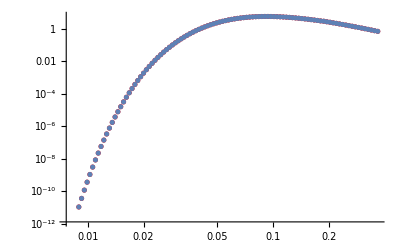

```mathematica
Show[
ListLogLogPlot[{Table[S[[i]],{i,300,400}]}, PlotStyle->Red],
ListLogLogPlot[{Table[S0[[i]],{i,300,400}]}]
]
```